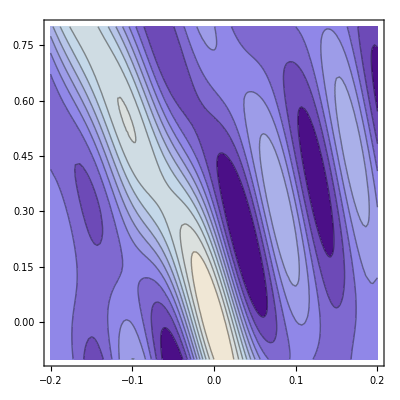

```mathematica
FC[qx_,qz_]:=x0/λr*Sin[w[qx,qz]]/w[qx,qz]+(λr-x0)/λr*Cos[0.5(0.5qx λr+w[qx,qz])]/Cos[0.5(0.5qx λr-w[qx,qz])]*Sin[0.5qx λr-w[qx,qz]]/(0.5qx λr-w[qx,qz])
w[qx_,qz_]:=0.5(qx x0+qz A)
x0=100;
A=20;
λr=145;
xmin=-0.2;xmax=0.2;
zmin=-0.1;zmax=0.8;
ContourPlot[FC[x,z],{x,xmin,xmax},{z,zmin,zmax},Contours->10]
```

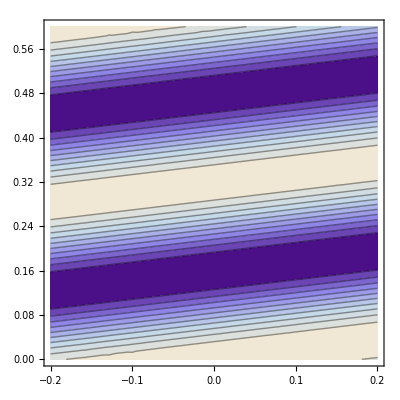

```mathematica
FT[qx_,qz_]:=RHM Cos[qz Xh Cos[ψ]-qx Xh Sin[ψ]]-1
ψ=10*π/180;
RHM=2.2;
Xh=20;
xmin=-0.2;xmax=0.2;
zmin=0;zmax=0.6;
ContourPlot[FT[x,z],{x,xmin,xmax},{z,zmin,zmax},Contours->10]
```